```mathematica
Detector[h_,w_] = {FaceForm[],EdgeForm[Black],Circle[{0,0},20],Rectangle[-1/2{h,w},1/2{h,w}]}
```

{FaceForm[],EdgeForm[GrayLevel[0]],Circle[{0,0},20],Rectangle[{-h/2,-w/2},{h/2,w/2}]}

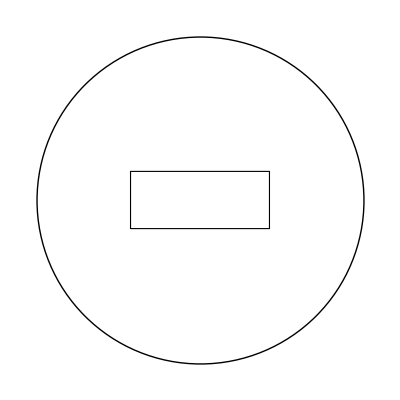

```mathematica
Graphics[{Detector[17,7]}]
```

```mathematica
DistributeOnCircle[g_, r_, n_, phi_: 0]:=Module[{dphi=2 Pi/n, gt = Translate[g,{r,0}]},
Table[Rotate[gt,dphi*i+phi,{0,0}],{i,0,n-1}]
]
```

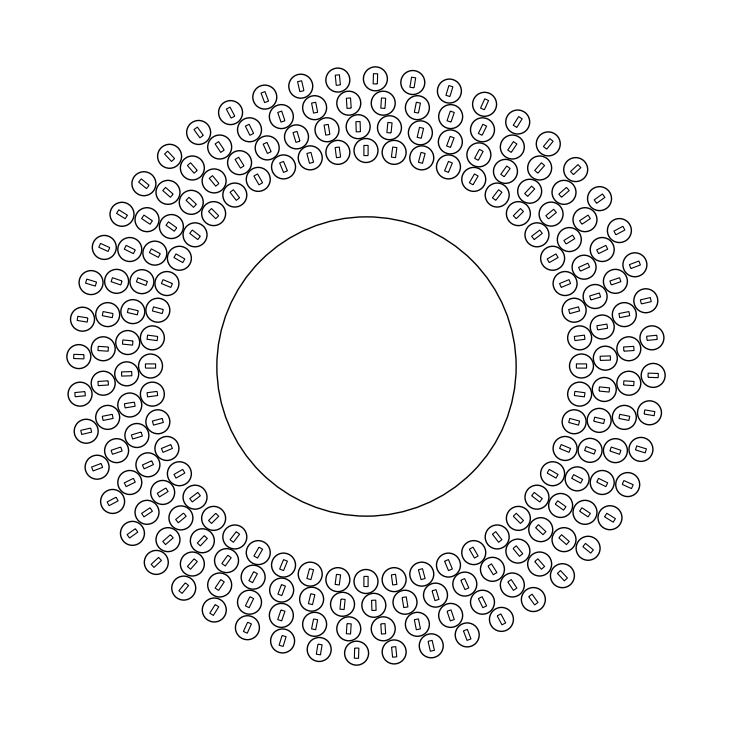

```mathematica
Join[
DistributeOnCircle[Detector[17,7],360,48]
,DistributeOnCircle[Detector[17,7],400,48, 1/4 2 Pi/48]
,DistributeOnCircle[Detector[17,7],440,48, 2/4 2 Pi/48]
,DistributeOnCircle[Detector[17,7],480,48, 3/4 2 Pi/48],
{Circle[{0,0},250]}
]//Graphics
```